Exercício 1

```mathematica
(*Começo importando os dados e o diretório do notebook*)
SetDirectory[NotebookDirectory[]];
brutoAl=Import["dados_Al.dat"]
brutoPb=Import["dados_Pb.dat"]
```

{{20,0.23},{40,2.09},{60,5.77},{80,9.65},{100,13.04},{150,18.52},{200,21.58},{250,23.25},{300,24.32}}

{{20,11.01},{40,19.57},{60,22.43},{80,23.69},{100,24.43},{150,25.27},{200,25.87},{250,26.36},{300,26.82}}

```mathematica
(*Faço o tratamento dos dados da segunda coluna dos arquivos obtidos*)
R=8.31;(*J/(mol K)*)

(*Alumínio*)
auxiliarAl=brutoAl//Transpose (*Faço uma transposição para obter os conjuntos de dados de temperatura e calor específico individualmente*)
```

{{20,40,60,80,100,150,200,250,300},{0.23,2.09,5.77,9.65,13.04,18.52,21.58,23.25,24.32}}

```mathematica
auxiliarAl[[2]]=auxiliarAl[[2]]/R (*Divido os dados da segunda coluna por R para ajustar as unidades*)
```

{0.0276775,0.251504,0.694344,1.16125,1.56919,2.22864,2.59687,2.79783,2.92659}

```mathematica
dadosAl=auxiliarAl//Transpose  (*Aplico a transposição novamente para reobter os pares ordenados*)
```

{{20,0.0276775},{40,0.251504},{60,0.694344},{80,1.16125},{100,1.56919},{150,2.22864},{200,2.59687},{250,2.79783},{300,2.92659}}

```mathematica
(*Aplico agora o mesmo raciocínio para os dados do Chumbo*)
auxiliarPb=brutoPb//Transpose
```

{{20,40,60,80,100,150,200,250,300},{11.01,19.57,22.43,23.69,24.43,25.27,25.87,26.36,26.82}}

```mathematica
auxiliarPb[[2]]=auxiliarPb[[2]]/R
```

{1.32491,2.35499,2.69916,2.85078,2.93983,3.04091,3.11312,3.17208,3.22744}

```mathematica
dadosPb=auxiliarPb//Transpose
```

{{20,1.32491},{40,2.35499},{60,2.69916},{80,2.85078},{100,2.93983},{150,3.04091},{200,3.11312},{250,3.17208},{300,3.22744}}

```mathematica
(*Uma vez obtidos os dados ajustados, construo os plots c/kB x T ou, nesse caso, c/R x T*)
```

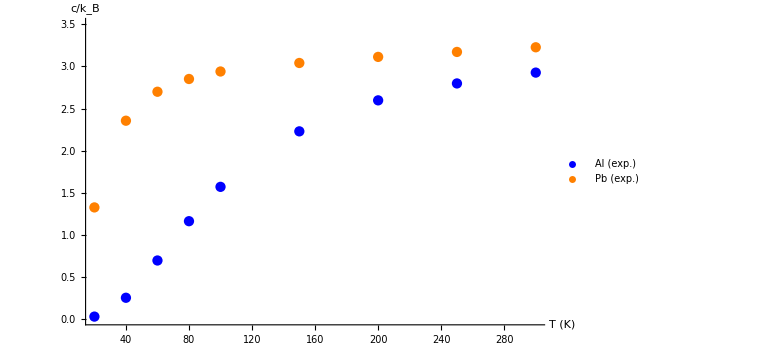

```mathematica
visual={ImageSize->Large,LabelStyle->{Large,Black}};
plotAl=ListPlot[
dadosAl,
PlotLegends->{"Al (exp.)"},
Evaluate[visual],
PlotStyle->{Blue}
];
plotPb=ListPlot[
dadosPb,
PlotLegends->{"Pb (exp.)"},
Evaluate[visual],
PlotStyle->{Orange}
];
Show[plotAl,plotPb, AxesLabel->{"T (K)","c/k_B"},Evaluate[visual],PlotRange->{0,3.5}]
```

```mathematica
(*Defino a função de energia interna correspondente ao modelo de Einstein e construo um ajuste do modelo*)

ℏ=Subscript[k, B]=1;
u[T_]:=3/2*(ℏ ω)/Subscript[k, B]*(Exp[(ℏ ω)/(Subscript[k, B] T)]+1)/(Exp[(ℏ ω)/(Subscript[k, B] T)]-1);
```

```mathematica
(*Faço os ajustes correspondentes a cada sólido. Para isso, verifico qual é a função c(T) correspondente ao calor específico. *)
D[u[T],T]//FullSimplify
```

(3 ω^2 Csch[ω/(2 T)]^2)/(4 T^2)

```mathematica
c[T_]:=(3 ω^2 Csch[ω/(2 T)]^2)/(4 T^2);
```

```mathematica
(*Das duas listas de dados apresentadas no gráfico anterior, extraio as coordenadas em que c é aproximadamente 1.5 para ambos os sólidos.*)
CoordenadasAuxiliares={{24.286750483559004,1.4950546983874995},{94.77756286266926,1.4950546983874995}};
Subscript[ω, Pb]=CoordenadasAuxiliares[[1,1]]
Subscript[ω, Al]=CoordenadasAuxiliares[[2,1]]
```

24.2868

94.7776

```mathematica
(*Construo os ajutes considerando as estimativas anteriores de frequência característica para cada sólido*)
ajusteAl=NonlinearModelFit[dadosAl,c[T],{{ω,Subscript[ω, Al]}},T];
ajusteAl["BestFitParameters"]
ajusteAl["ParameterErrors"]
ajusteAl["AdjustedRSquared"]
```

{ω→276.714}

{5.91068}

0.998263

```mathematica
ajustePb=NonlinearModelFit[dadosPb,c[T],{{ω,Subscript[ω, Pb]}},T];
ajustePb["BestFitParameters"]
ajustePb["ParameterErrors"]
ajustePb["AdjustedRSquared"]
```

{ω→65.5686}

{3.49105}

0.997995

```mathematica
(*Construo os gráficos de ajuste*)
```

```mathematica
Chop[ajusteAl];
Chop[ajustePb];
```

General::munfl: Csch[22575.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Csch[5349.42] is too small to represent as a normalized machine number; precision may be lost.

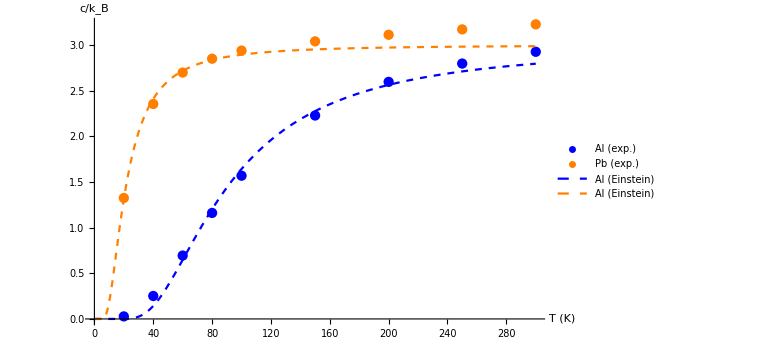

```mathematica
PlotAjusteAl=Plot[
c[T]/.ajusteAl["BestFitParameters"],
{T,0,300},
PlotStyle->{Dashed,Blue},
PlotLegends->{"Al (Einstein)"},
Evaluate[visual],
PlotRange->{{0,300},{0,3.5}}
];
PlotAjustePb=Plot[
c[T]/.ajustePb["BestFitParameters"],
{T,0,300},
PlotStyle->{Dashed,Orange},
PlotLegends->{"Al (Einstein)"},
Evaluate[visual],
PlotRange->{{0,300},{0,3.5}}
];

Show[plotAl,plotPb,PlotAjusteAl,PlotAjustePb,AxesLabel->{"T (K)","c/k_B"},PlotRange->All]
```

```mathematica
(*Defino a função de Debye*)
Clear[c];
c[T_]:=9 Subscript[k, B](T/TD)^3 Integrate[(η^4 ⅇ^η)/((ⅇ^η-1)^2),{η,.01,.99TD/T}];
```

```mathematica
(*Refaço os ajustes usando as mesmas definições de T^* e palpite de parâmetros*)
Clear[ajusteAl,ajustePb];
ajusteAl=NonlinearModelFit[dadosAl,c[T],{{TD,Subscript[ω, Al]}},T];
ajusteAl["BestFitParameters"]
ajusteAl["ParameterErrors"]
ajusteAl["AdjustedRSquared"]
```

NonlinearModelFit::nrlnum: The function value {1.15646-3.84579×10^-14 ⅈ,1.99284-5.76869×10^-14 ⅈ,1.88951+3.24489×10^-14 ⅈ,«3»,0.282213-7.88688×10^-13 ⅈ,0.0926086-1.46705×10^-13 ⅈ,-0.0299806+9.66495×10^-13 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {94.7776}.

NonlinearModelFit[{{20,0.0276775},{40,0.251504},{60,0.694344},{80,1.16125},{100,1.56919},{150,2.22864},{200,2.59687},{250,2.79783},{300,2.92659}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,94.7776}},T][BestFitParameters]

NonlinearModelFit::nrlnum: The function value {1.15646-3.84579×10^-14 ⅈ,1.99284-5.76869×10^-14 ⅈ,1.88951+3.24489×10^-14 ⅈ,«3»,0.282213-7.88688×10^-13 ⅈ,0.0926086-1.46705×10^-13 ⅈ,-0.0299806+9.66495×10^-13 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {94.7776}.

NonlinearModelFit[{{20,0.0276775},{40,0.251504},{60,0.694344},{80,1.16125},{100,1.56919},{150,2.22864},{200,2.59687},{250,2.79783},{300,2.92659}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,94.7776}},T][ParameterErrors]

NonlinearModelFit::nrlnum: The function value {1.15646-3.84579×10^-14 ⅈ,1.99284-5.76869×10^-14 ⅈ,1.88951+3.24489×10^-14 ⅈ,«3»,0.282213-7.88688×10^-13 ⅈ,0.0926086-1.46705×10^-13 ⅈ,-0.0299806+9.66495×10^-13 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {94.7776}.

NonlinearModelFit[{{20,0.0276775},{40,0.251504},{60,0.694344},{80,1.16125},{100,1.56919},{150,2.22864},{200,2.59687},{250,2.79783},{300,2.92659}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,94.7776}},T][AdjustedRSquared]

```mathematica
ajustePb=NonlinearModelFit[dadosPb,c[T],{{TD,.9 Subscript[ω, Pb]}},T];
ajustePb["BestFitParameters"]
ajustePb["ParameterErrors"]
ajustePb["AdjustedRSquared"]
```

NonlinearModelFit::nrlnum: The function value {1.42247+0. ⅈ,0.51373+8.57285×10^-14 ⅈ,0.192833+7.02667×10^-13 ⅈ,0.0493464-«1»,«1»,«1»,-0.206221-2.22932×10^-11 ⅈ,-0.266764+5.11565×10^-12 ⅈ,-0.325053-1.55×10^-11 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {21.8581}.

NonlinearModelFit[{{20,1.32491},{40,2.35499},{60,2.69916},{80,2.85078},{100,2.93983},{150,3.04091},{200,3.11312},{250,3.17208},{300,3.22744}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,21.8581}},T][BestFitParameters]

NonlinearModelFit::nrlnum: The function value {1.42247+0. ⅈ,0.51373+8.57285×10^-14 ⅈ,0.192833+7.02667×10^-13 ⅈ,0.0493464-«1»,«1»,«1»,-0.206221-2.22932×10^-11 ⅈ,-0.266764+5.11565×10^-12 ⅈ,-0.325053-1.55×10^-11 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {21.8581}.

NonlinearModelFit[{{20,1.32491},{40,2.35499},{60,2.69916},{80,2.85078},{100,2.93983},{150,3.04091},{200,3.11312},{250,3.17208},{300,3.22744}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,21.8581}},T][ParameterErrors]

NonlinearModelFit::nrlnum: The function value {1.42247+0. ⅈ,0.51373+8.57285×10^-14 ⅈ,0.192833+7.02667×10^-13 ⅈ,0.0493464-«1»,«1»,«1»,-0.206221-2.22932×10^-11 ⅈ,-0.266764+5.11565×10^-12 ⅈ,-0.325053-1.55×10^-11 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {21.8581}.

NonlinearModelFit[{{20,1.32491},{40,2.35499},{60,2.69916},{80,2.85078},{100,2.93983},{150,3.04091},{200,3.11312},{250,3.17208},{300,3.22744}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,21.8581}},T][AdjustedRSquared]

```mathematica
(*Construo os gráficos e anexo todas as curvas construídas em uma única figura*)
PlotAjusteAlDebye[
c[T]/.ajusteAl["BestFitParameters"],
{T,.01,300},
Evaluate[visual],
PlotStyle->{Blue},
PlotLegends->{"Al (Debye)"}
]
PlotAjustePbDebye[
c[T]/.ajustePb["BestFitParameters"],
{T,.01,300},
Evaluate[visual],
PlotStyle->{Orange},
PlotLegends->{"Pb (Debye)"}
]
```

NonlinearModelFit::nrlnum: The function value {1.15646-3.84579×10^-14 ⅈ,1.99284-5.76869×10^-14 ⅈ,1.88951+3.24489×10^-14 ⅈ,«3»,0.282213-7.88688×10^-13 ⅈ,0.0926086-1.46705×10^-13 ⅈ,-0.0299806+9.66495×10^-13 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {94.7776}.

ReplaceAll::reps: {NonlinearModelFit[{{20,0.0276775},{40,0.251504},{60,0.694344},{80,1.16125},{100,1.56919},{150,2.22864},{200,2.59687},{250,2.79783},{300,2.92659}},ConditionalExpression[(«1»)/(«2»)^3,«1»],{{«1»}},T][…s]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PlotAjusteAlDebye[ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ]/.NonlinearModelFit[{{20,0.0276775},{40,0.251504},{60,0.694344},{80,1.16125},{100,1.56919},{150,2.22864},{200,2.59687},{250,2.79783},{300,2.92659}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,94.7776}},T][BestFitParameters],{T,0.01,300},{ImageSize→Large,LabelStyle→{Large,GrayLevel[0]}},PlotStyle→{RGBColor[0, 0, 1]},PlotLegends→{Al (Debye)}]

NonlinearModelFit::nrlnum: The function value {1.42247+0. ⅈ,0.51373+8.57285×10^-14 ⅈ,0.192833+7.02667×10^-13 ⅈ,0.0493464-«1»,«1»,«1»,-0.206221-2.22932×10^-11 ⅈ,-0.266764+5.11565×10^-12 ⅈ,-0.325053-1.55×10^-11 ⅈ} is not a list of real numbers with dimensions {9} at {TD} = {21.8581}.

ReplaceAll::reps: {NonlinearModelFit[{{20,1.32491},{40,2.35499},{60,2.69916},{80,2.85078},{100,2.93983},{150,3.04091},{200,3.11312},{250,3.17208},{300,3.22744}},«1»,{{TD,21.8581}},T][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PlotAjustePbDebye[ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ]/.NonlinearModelFit[{{20,1.32491},{40,2.35499},{60,2.69916},{80,2.85078},{100,2.93983},{150,3.04091},{200,3.11312},{250,3.17208},{300,3.22744}},ConditionalExpression[1/TD^3 9 T^3 (-25.9758+TD^4/((-1.04102+1.04102 ⅇ^(-(0.99 TD)/T)) T^4)+(3.8812 TD^3 Log[1.-1. ⅇ^((0.99 TD)/T)])/T^3+(TD (11.7612 TD PolyLog[2.,ⅇ^((0.99 TD)/T)]-23.76 T PolyLog[3.,ⅇ^((0.99 TD)/T)]))/T^2+24. PolyLog[4.,ⅇ^((0.99 TD)/T)]),Re[TD/T]>6.×10^-23||TD/T∉ℝ],{{TD,21.8581}},T][BestFitParameters],{T,0.01,300},{ImageSize→Large,LabelStyle→{Large,GrayLevel[0]}},PlotStyle→{RGBColor[1, 0.5, 0]},PlotLegends→{Pb (Debye)}]

Exercício 2

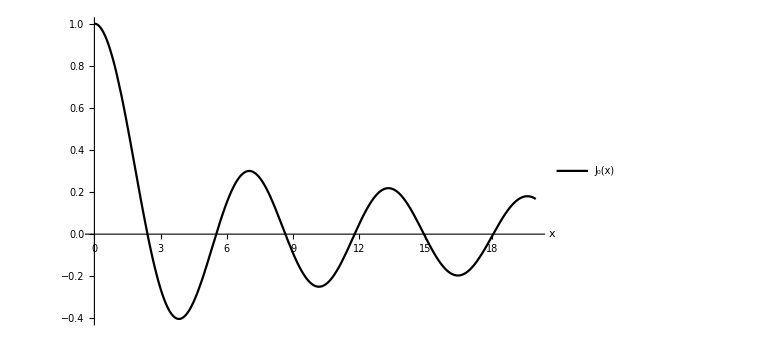

```mathematica
(*Construindo um gráfico de Subscript[J, 0](x)*)
Plot[
BesselJ[0,x],
{x,0,20},
Evaluate[visual],
PlotStyle->Black,
AxesLabel->{"x",""},
PlotLegends->{"J_0(x)"}
]
```

```mathematica
(*Utilizo a função "GetCoordinates" para verificar quais são as coordenadas aproximadas das raízes. Esse resultado será útil como um palpite inicial para as iterações do método de Newton-Raphson*)
coordenadas={{2.3448844884488453,0.0061477106912248836},{5.579207920792078,-0.003640265055598224},{8.692244224422442,-0.003640265055598224},{11.886138613861384,0.0061477106912248836},{14.877887788778875,-0.003640265055598224},{18.152640264026402,-0.003640265055598224}};
coordenadasX=Table[coordenadas[[n,1]],{n,1,Length[coordenadas]}]
```

{2.34488,5.57921,8.69224,11.8861,14.8779,18.1526}

```mathematica
(*Defino a função que será iterada na busca pelas raízes*)
f[x_]=x-BesselJ[0,x]/D[BesselJ[0,x],x];
```

```mathematica
(* Verifico a estimativa de cada raiz com o auxílio da função FixedPoint, realizando iterações até que o erro entre duas saídas consecutivas seja menor que 10^-10*)

raizes=Table[FixedPoint[f,coordenadasX[[n]],SameTest->(Abs[#1-#2]<1*^-10&)],{n,1,Length[coordenadasX]}]
```

{2.40483,5.52008,8.65373,11.7915,14.9309,18.0711}

```mathematica
(* Apenas como uma forma de validação do resultado obtido, faço uma busca por raízes utilizando a função FindRoot*)
Table[FindRoot[BesselJ[0,x],{x,n}],{n,1,17}]
```

{{x→2.40483},{x→2.40483},{x→2.40483},{x→8.65373},{x→5.52008},{x→5.52008},{x→-52.6241},{x→8.65373},{x→8.65373},{x→8.65373},{x→11.7915},{x→11.7915},{x→11.7915},{x→14.9309},{x→14.9309},{x→14.9309},{x→18.0711}}

```mathematica
(*É possível notar que a função não converge para os valores corretos em algumas situações. De fato, o método de obtenção de raízes empregado anteriormente é muito mais eficiente. Permite que a precisão da convergência seja escolhida pelo próprio usuário (comando SameTest) e exige um baixo custo de computacional*)
```

```mathematica
ClearAll["Global`*"]
```